# Phase Transition under High-T Expansion

```mathematica
ClearAll["Global`*"]
```

## Analytical Calculation

### Expression for critical temperature

This section calculates the formula for critical temperature.

```mathematica
$Assumptions={{Dterm,h,Eterm,T,λterm,T0}∈PositiveReals};
Vana=Dterm (T^2-T0^2)h^2-Eterm T h^3+1/4 λterm h^4;(*General form of high-T potential*)
hmin=h/.(Solve[D[Vana,h]==0,h]//Normal)[[2]]//Simplify(*Non-zero local minimum*)
Tcana=T/.Solve[(Vana/.{h->hmin}//Simplify)==0,T]//Normal//Simplify(*Critical temperature*)
hoverT=hmin/Tc/.{T->Tc}//Simplify
```

(3 Eterm T+√(9 Eterm^2 T^2+8 Dterm (-T^2+T0^2) λterm))/(2 λterm)

{T0 √((Dterm λterm)/(-Eterm^2+Dterm λterm))}

(3 Eterm Tc+√(9 Eterm^2 Tc^2+8 Dterm (T0^2-Tc^2) λterm))/(2 Tc λterm)

### Expression for eliminating S

```mathematica
$Assumptions={{Dterm,h,Eterm,T,λterm,T0,μH,A,μS,cs,S,v}∈PositiveReals};
VwithS=Dterm T^2 h^2-1/2 μH^2 h^2-Eterm T h^3+1/4 λterm h^4+1/2 μS^2 S^2-1/2 A(h^2+cs T^2-2 v^2)S;
Svev=S/.Solve[D[VwithS,S]==0,S]//Normal//Simplify
Dprime=Coefficient[VwithS/.{S->Svev},h,2]//Simplify
Eprime=Coefficient[VwithS/.{S->Svev},h,3]//Simplify
λprime=Coefficient[VwithS/.{S->Svev},h,4]//Simplify
VwithS/.{S->Svev}//FullSimplify
```

{(A (h^2+cs T^2-2 v^2))/(2 μS^2)}

{1/4 (4 Dterm T^2-2 μH^2+(A^2 (-cs T^2+2 v^2))/μS^2)}

{-Eterm T}

{λterm/4-A^2/(8 μS^2)}

{1/4 h^2 (-4 Eterm h T+4 Dterm T^2+h^2 λterm-2 μH^2)-(A^2 (h^2+cs T^2-2 v^2)^2)/(8 μS^2)}

```mathematica
(Dprime h^2+Eprime h^3+λprime h^4-(VwithS/.{S->Svev}))//FullSimplify(*Check whether we have some remaining terms*)
```

{(A^2 (cs T^2-2 v^2)^2)/(8 μS^2)}

This is field-independent, and can be ignored.

## Define V_eff in high-T with physical parameters

```mathematica
g=0.65;
gY=0.36;
yt=0.9945;
DSM=1/16(3 g^2+gY^2+4 yt^2);
ESM=1/(48π)(2 g^3+(g^2+gY^2)^(3/2));
cs=1/3;
mh=125.13;
GF = 1.16637 *10^-5;
v=1/(√(2 √2*GF));
μH2[mS_,sinθ_]:=1/2(mh^2(1-sinθ^2)+mS^2 sinθ^2);
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A[mS_,sinθ_]:=((mh^2-mS^2)sinθ √(1-sinθ^2))/(√2 v);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
VhighT2d[mS_,sinθ_,h_,S_,T_]:=DSM T^2 h^2-1/2 μH2[mS,sinθ] h^2-ESM T h^3+1/4 λ[mS,sinθ] h^4+1/2 μS2[mS,sinθ] S^2-1/2 A[mS,sinθ](h^2+cs T^2-2 v^2)S;
Deff[mS_,sinθ_]:=DSM- (cs A[mS,sinθ]^2)/(4μS2[mS,sinθ]);
λeff[mS_,sinθ_]:=λ[mS,sinθ]-A[mS,sinθ]^2/(2 μS2[mS,sinθ]);
T0[mS_,sinθ_]:=√((1/2 μH2[mS,sinθ]-(v^2 A[mS,sinθ]^2)/(2μS2[mS,sinθ]))/(DSM- (cs A[mS,sinθ]^2)/(4μS2[mS,sinθ])));
Tc[mS_,sinθ_]=T0[mS,sinθ] √((Deff[mS,sinθ] λeff[mS,sinθ])/(-ESM^2+Deff[mS,sinθ] λeff[mS,sinθ]));
strength[mS_,sinθ_]=(2ESM)/λeff[mS,sinθ];
VhighT[mS_,sinθ_,h_,T_]:=Deff[mS,sinθ] T^2 h^2+(-1/2 μH2[mS,sinθ]+(v^2 A[mS,sinθ]^2)/(2μS2[mS,sinθ]))h^2-ESM T h^3+1/4 λeff[mS,sinθ] h^4;
Positive‵factor[mS_,sinθ_]=-ESM^2+Deff[mS,sinθ] λeff[mS,sinθ];
```

Check whether the minimum is successfully found.

```mathematica
strength[5,0.17]*Tc[5,0.17]
FindRoot[{D[VhighT2d[5,0.17,h,S,Tc[5,0.17]],h]==0,D[VhighT2d[5,0.17,h,S,Tc[5,0.17]],S]==0},{{h,100},{S,700}}]
hc=h/.FindRoot[D[VhighT[5,0.17,h,Tc[5,0.17]],h]==0,{h,100}]
VhighT[5,0.17,0,Tc[5,0.17]]
VhighT[5,0.17,hc,Tc[5,0.17]]
```

48.4501

{h→48.4501,S→-647.563}

48.4501

0.

-5.82077×10^-11

Success!

## Plots

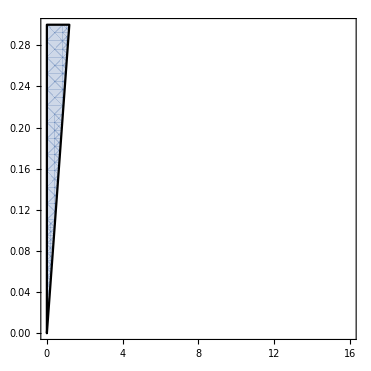

```mathematica
RegionPlot[-ESM^2+Deff[mS,sinθ] λeff[mS,sinθ]<=0,{mS,0,16},{sinθ,0,0.3}]
```

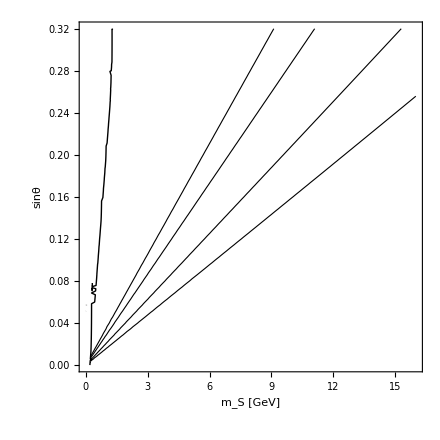

```mathematica
ContourPlot[Tc[mS,sinθ],{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},Contours->{25,30,40,50},ContourShading->None]
```

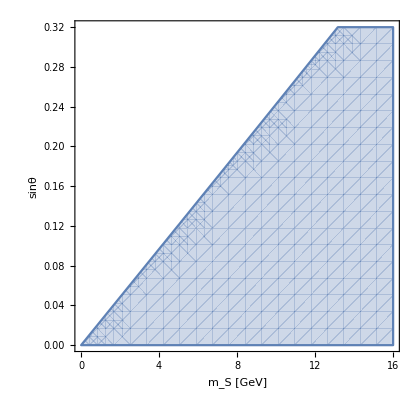

```mathematica
RegionPlot[strength[mS,sinθ]≤1.,{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},BoundaryStyle->ColorData[97,"ColorList"][[1]]]
```

## Output

```mathematica
DumpSave[NotebookDirectory[]<>"/output/highT.m",{strength,Tc,Positive‵factor}];
```